```mathematica
Clear["Global`*"]
```

```mathematica
θ=HeavisideTheta
```

HeavisideTheta

```mathematica
imchi=(√(2m))^d/(2^d π^((d-1)/2)Gamma[(d+1)/2] √ϵq)(θ[μ-(ω-ϵq)^2/(4ϵq)](μ-(ω-ϵq)^2/(4ϵq))^((d-1)/2)-θ[μ-(ω+ϵq)^2/(4ϵq)](μ-(ω+ϵq)^2/(4ϵq))^((d-1)/2))/.{ϵq->q^2/(2m)}/.{m->1,μ->1};
```

```mathematica
imχ[q_,ω_,d_]:=Evaluate[imchi]
```

```mathematica
Manipulate[Plot[imχ[q,ω,d],{q,0,5},Exclusions->None,PlotRange->{All,{0,1.5}}],{ω,0,3},{d,1,5,1}]
```

```mathematica
{imχ[1,1,3],imχ[1,-1,3]}
```

{7/(16 π),-7/(16 π)}

# d=1

```mathematica
Plot3D[imχ[q,ω,1],{q,0,5},{ω,0,2.5}]
```

-Graphics3D-

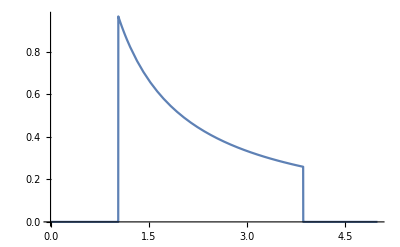

```mathematica
Plot[imχ[q,2,1],{q,0,5},Exclusions->None]
```

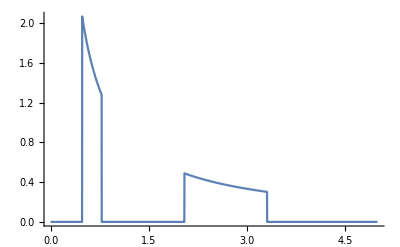

```mathematica
Plot[imχ[q,0.8,1],{q,0,5},Exclusions->None,PlotRange->All]
```

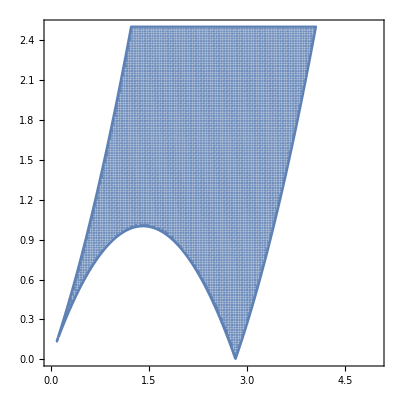

```mathematica
RegionPlot[imχ[q,ω,1]>0,{q,0,5},{ω,0,2.5}
,PerformanceGoal->"Quality",PlotPoints->200]
```

# d=2

```mathematica
Plot3D[imχ[q,ω,2],{q,0,5},{ω,0,2.5}]
```

-Graphics3D-

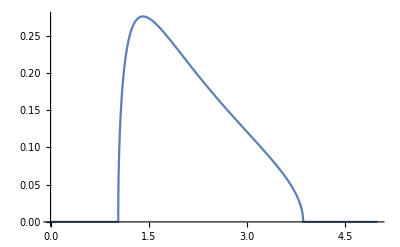

```mathematica
Plot[imχ[q,2,2],{q,0,5},Exclusions->None]
```

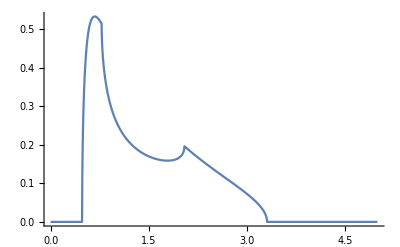

```mathematica
Plot[imχ[q,0.8,2],{q,0,5},Exclusions->None,PlotRange->All]
```

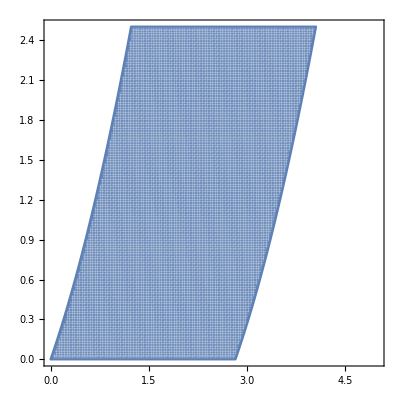

```mathematica
RegionPlot[imχ[q,ω,2]>0,{q,0,5},{ω,0,2.5}
,PerformanceGoal->"Quality",PlotPoints->200]
```

# d=3

```mathematica
Plot3D[imχ[q,ω,3],{q,0,5},{ω,0,2.5}]
```

-Graphics3D-

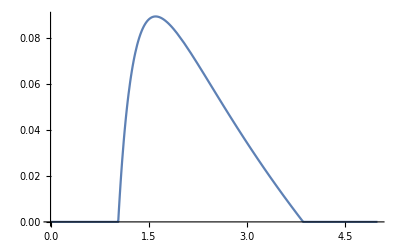

```mathematica
Plot[imχ[q,2,3],{q,0,5},Exclusions->None]
```

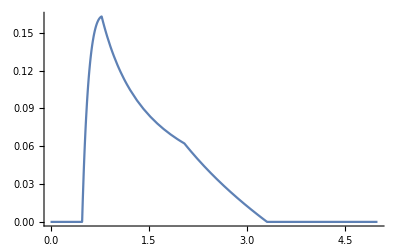

```mathematica
Plot[imχ[q,0.8,3],{q,0,5},Exclusions->None,PlotRange->All]
```

```mathematica
RegionPlot[imχ[q,ω,3]>0,{q,0,5},{ω,0,2.5}
,PerformanceGoal->"Quality",PlotPoints->200]
```

-Graphics-

```mathematica
ContourPlot[imχ[q,ω,3],{q,0,5},{ω,0,2.5}
,PerformanceGoal->"Quality",PlotPoints->200]
```

-Graphics-

```mathematica
RegionPlot[imχ[q,ω,3]>0,{q,0,20},{ω,0,20}
,PerformanceGoal->"Quality",PlotPoints->200]
```